## Import dependency

```mathematica
SetDirectory[NotebookDirectory[]]
PacletDirectoryAdd[{"/Users/ianfan/Downloads/WolframSummerSchoolRL-master"}];
<<WolframSummerSchoolRL`;
PacletDirectoryAdd[{"/Users/ianfan/Downloads/neuralnetworks"}]
<<NeuralNetworks`
Lookup[PacletInformation@"NeuralNetworks","Version"]
Get["RLproject-pong-q-duo.wl"]
Get["/Users/ianfan/Documents/gym-http-api/binding-wl/gym_http_client.wl"];
```

/Users/ianfan/Documents/gym-http-api/binding-wl

{/Users/ianfan/Downloads/WolframSummerSchoolRL-master,/Users/ianfan/Downloads/neuralnetworks}

11.3.7

## Init Environment

```mathematica
$env=RLEnvironmentCreate["WLCartPole"]
```

## Close Environment

```mathematica
RLEnvironmentClose[$env]
```

## Init Net

```mathematica
policyNet=NetInitialize@NetChain[{LinearLayer[128],Tanh,LinearLayer[128],Tanh,LinearLayer[2]},"Input"->8,"Output"->NetDecoder[{"Class",{0,1}}]];
```

## Performance of the init net

```mathematica
data = preprocess[game[10,10000,policyNet,True,0,$env]];
Length[data["reward"]]
```

## Init generator

```mathematica
generator := creatGenerator[$env, 20, 10000, False, 0.98, 1000, 0.95, False]
```

## Training

```mathematica
trained = NetTrain[policyNet, generator,LossFunction->MeanSquaredLossLayer[],BatchSize->32,MaxTrainingRounds->2000]
```

NetChain[<>]

## Plot the reward received during the training

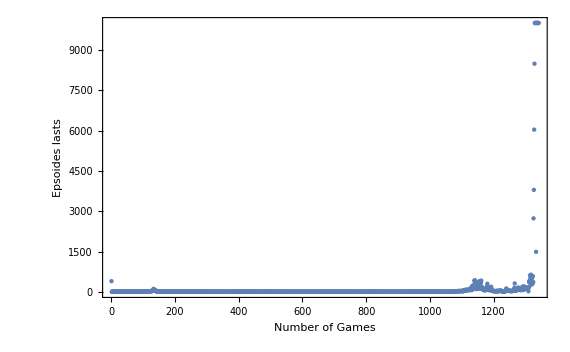

```mathematica
$rewardList;
ListPlot[$rewardList,PlotRange->All,Frame->True, FrameLabel->{"Number of Games","Epsoides lasts"}]
```

## Result of the best net

```mathematica
bN = getBest[];
data = preprocess[game[1,10000,bN,True,0,$env]];
Length[data["action"]]
```

10000

## Result of the trained net

```mathematica
data = preprocess[game[10,10000,trained,True,0,$env]];
Length[data["action"]]
```

100000

## Test on generator

```mathematica
data =generator[<|"AbsoluteBatch"->0,"BatchSize"->12,"Net"->policyNet|>];
```

## Form animation

```mathematica
re = {};

ob = RLEnvironmentReset[$env];
pre = ob;
Do[
pre = Join[ob,pre];
action = net[pre];
pre = ob;
state = RLEnvironmentStep[$env, action, True];
ob = state["Observation"];
AppendTo[re,state["Rendering"]];
If[state["Done"],Break[]];
,{step,10000}];
```

```mathematica
ListAnimate[re[[;;500]],120]
```

## Form picture of the environment

```mathematica
$env=RLEnvironmentCreate["Breakout-v0"];
RLEnvironmentReset[$env]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},124,{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}},209}
 |  |  |  |

```mathematica
Do[data = RLEnvironmentStep[$env,1,False],1]
```

```mathematica
Image[data["Observation"],"Byte"]
```

-Graphics-